# QED calculation: Peskin Sec. 5

## e^-μ^-→e^-μ^- (QED): Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (21 Feb 2018)

by Thomas Hahn

### Create Topology

```mathematica
topologies=CreateTopologies[0,2->2];
(*Paint[topologies];*)
```

### Insert Particles

Appendix B of the FeynArts manual contains a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes}];
```

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 4 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

> Top. 1: 4 diagrams

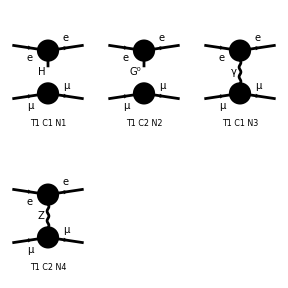

```mathematica
Paint[diagrams];
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

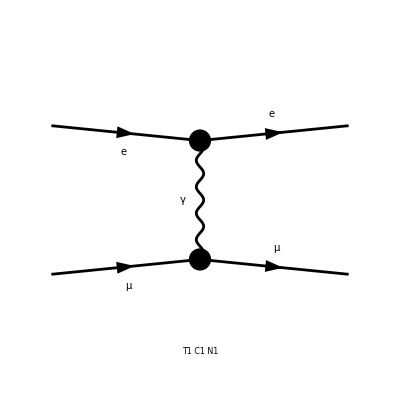

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}}}→{{F[2,{1}],k[3],ME,{-Charge,LeptonNumber}},{F[2,{2}],k[4],MM,{-Charge,LeptonNumber}}}][4 Alfa π Den[T,0] Mat[F1]-4 Alfa π Den[T,0] Mat[F2]+2 Alfa π Den[T,0] Mat[F3]-2 Alfa π Den[T,0] Mat[F4]]

HelicityME returns AVERAGE!

```mathematica
(*Note that, in FormCalc v9.6 (and later),
 SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
{squared,squaredRules}=SquaredME[amplitude]
helSquared=squared//.HelicityME[amplitude]
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-4 Alfa π Den[T,0],FF[F3]→2 Alfa π Den[T,0],FF[F4]→-2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-4 Alfa π Den[T,0],FFC[F3]→2 Alfa π Den[T,0],FFC[F4]→-2 Alfa π Den[T,0]}}

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

FF[F3] (FFC[F1] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U))-1/2 (Abb14 ME2-2 Abb16 ME MM+Abb13 MM2) Hel[1] Hel[2]+(ME+MM) (Eps3 Hel[1]+Eps12 Hel[2])+(Eps4 (ME+MM)-(Abb18 ME-Abb17 MM) Hel[1] Hel[2]+1/4 (Abb27 Hel[1]+Abb33 Hel[2])) Hel[3]+(Eps7 (ME+MM)-(Abb22 ME-Abb20 MM) Hel[1] Hel[2]+1/4 (Abb28 Hel[1]+Abb31 Hel[2])+(1/2 (-Abb34 ME2+2 Abb32 ME MM-Abb35 MM2)-(Abb23 ME+Abb21 MM) Hel[1]-(Abb29 ME+Abb30 MM) Hel[2]-1/2 (Abb24 ME2-2 Abb26 ME MM+Abb19 MM2) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F3] (1/2 (ME2^2+14 ME2 MM2+MM2^2-4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U))+(Abb82 ME2+2 Abb81 ME MM+Abb80 MM2) Hel[2] Hel[3]+Hel[1] ((Abb70-2 (Abb67 ME MM+ME2 MM2 Pair1)) Hel[2]+(Abb74 ME2+2 Abb72 ME MM+Abb71 MM2) Hel[3])+((Abb78 ME2+2 Abb79 ME MM+Abb77 MM2) Hel[1]+(Abb85 ME2+2 Abb84 ME MM+Abb83 MM2) Hel[2]+(Abb88-2 (Abb86 ME MM+ME2 MM2 Pair4)+1/2 (Abb92-4 Abb76 ME MM+4 Abb69 ME2 MM2) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F2] ((1/4 (Abb58+4 (Abb48 ME MM+ME2 MM2 Pair18)) Hel[1]+(1/4 (-Abb65-4 (Abb54 ME MM+ME2 MM2 Pair15))-1/2 ((Abb36+2 Eps17 ME2) MM+ME (Abb37+2 Eps15 MM2)) Hel[1]) Hel[2]) Hel[3]+(-1/4 (Abb60+4 (Abb52 ME MM+ME2 MM2 Pair16)) Hel[1]+(1/4 (Abb66+4 (Abb62 ME MM+ME2 MM2 Pair17))+1/2 ((Abb38+2 Eps21 ME2) MM+ME (Abb40+2 Eps19 MM2)) Hel[1]) Hel[2]+(1/2 ((Abb49+2 Eps25 ME2) MM+ME (Abb50+2 Eps23 MM2)) Hel[1]-1/2 ((Abb55+2 Eps29 ME2) MM+ME (Abb56+2 Eps27 MM2)+(Abb42 ME2-2 Abb46 ME MM+Abb43 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F4] (1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U))-2 (Eps3 MM Hel[1]+Eps12 ME Hel[2])-((Abb103 ME2-Abb71 MM2) Hel[1]+(2 Abb111 ME MM-1/2 (Abb97 ME+Abb98 MM+4 Eps31 ME MM2) Hel[1]) Hel[2]) Hel[3]-MM (-2 Abb93 ME Hel[1] Hel[2]+2 Eps4 Hel[3])-(2 ME (Eps7+Abb109 MM Hel[1])+(-Abb85 ME2+Abb112 MM2-1/2 (Abb102 ME+(Abb100-4 Eps32 ME2) MM) Hel[1]) Hel[2]+(2 Abb120 ME MM-1/2 (Abb107 ME-Abb105 MM-4 Eps33 ME MM2) Hel[1]+1/2 (Abb116 ME-(Abb115+4 Eps34 ME2) MM+(Abb125-4 Abb95 ME2 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4]))+FF[F2] (1/4 FFC[F2] (4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2-(Abb3-4 (Abb1 ME MM+ME2 MM2 Pair1)) Hel[1] Hel[2]-(Abb6-4 (Abb4 ME MM+ME2 MM2 Pair4)) Hel[3] Hel[4]+(Abb5+4 (Abb2 ME MM+ME2 MM2 Pair1 Pair4)) Hel[1] Hel[2] Hel[3] Hel[4])+FFC[F4] ((ME-MM) (-Eps3 Hel[1]+Eps12 Hel[2])+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)+(Abb14 ME2+2 Abb16 ME MM+Abb13 MM2) Hel[1] Hel[2])+(-Eps4 (ME-MM)+1/4 Abb27 Hel[1]+(-Abb33/4-(Abb18 ME+Abb17 MM) Hel[1]) Hel[2]) Hel[3]+(Eps7 (ME-MM)-1/4 Abb28 Hel[1]+(Abb31/4+(Abb22 ME+Abb20 MM) Hel[1]) Hel[2]+(1/2 (Abb34 ME2+2 Abb32 ME MM+Abb35 MM2)-(Abb23 ME-Abb21 MM) Hel[1]+(Abb29 ME-Abb30 MM-1/2 (Abb24 ME2+2 Abb26 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F3] ((1/4 (Abb58+4 (Abb48 ME MM+ME2 MM2 Pair18)) Hel[1]+(1/4 (-Abb65-4 (Abb54 ME MM+ME2 MM2 Pair15))+1/2 ((Abb36+2 Eps17 ME2) MM+ME (Abb37+2 Eps15 MM2)) Hel[1]) Hel[2]) Hel[3]+(-1/4 (Abb60+4 (Abb52 ME MM+ME2 MM2 Pair16)) Hel[1]+(1/4 (Abb66+4 (Abb62 ME MM+ME2 MM2 Pair17))-1/2 ((Abb38+2 Eps21 ME2) MM+ME (Abb40+2 Eps19 MM2)) Hel[1]) Hel[2]+(-1/2 ((Abb49+2 Eps25 ME2) MM+ME (Abb50+2 Eps23 MM2)) Hel[1]+(1/2 ((Abb55+2 Eps29 ME2) MM+ME (Abb56+2 Eps27 MM2))-1/2 (Abb42 ME2-2 Abb46 ME MM+Abb43 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F1] (-Pair5 (ME2 Pair2 Hel[1]+ME (MM Pair3-Eps1 Hel[1]) Hel[2]) Hel[3]-(Pair6 (ME MM Pair2 Hel[1]+(MM2 Pair3-Eps1 MM Hel[1]) Hel[2])+(-1/4 Abb12 Hel[1] Hel[2]+Eps2 (ME Pair2 Hel[1]+MM Pair3 Hel[2])) Hel[3]) Hel[4]))+FF[F1] (1/4 FFC[F1] (4 (ME2 MM2+ME MM (ME2+MM2-S))+(ME2+MM2-S)^2+(Abb3+4 Abb1 ME MM-4 ME2 MM2 Pair1) Hel[1] Hel[2]+(Abb6+4 Abb4 ME MM-4 ME2 MM2 Pair4+(Abb5-4 Abb2 ME MM+4 ME2 MM2 Pair1 Pair4) Hel[1] Hel[2]) Hel[3] Hel[4])+FFC[F3] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U))-1/2 (Abb14 ME2-2 Abb16 ME MM+Abb13 MM2) Hel[1] Hel[2]-(ME+MM) (Eps3 Hel[1]+Eps12 Hel[2])+(-Eps4 (ME+MM)+(Abb18 ME-Abb17 MM) Hel[1] Hel[2]+1/4 (Abb27 Hel[1]+Abb33 Hel[2])) Hel[3]+(-Eps7 (ME+MM)+(Abb22 ME-Abb20 MM) Hel[1] Hel[2]+1/4 (Abb28 Hel[1]+Abb31 Hel[2])+(1/2 (-Abb34 ME2+2 Abb32 ME MM-Abb35 MM2)+(Abb23 ME+Abb21 MM) Hel[1]+(Abb29 ME+Abb30 MM-1/2 (Abb24 ME2-2 Abb26 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F2] (-Pair5 (ME2 Pair2 Hel[1]+ME (MM Pair3+Eps1 Hel[1]) Hel[2]) Hel[3]-(Pair6 (ME MM Pair2 Hel[1]+(MM2 Pair3+Eps1 MM Hel[1]) Hel[2])+(-1/4 Abb12 Hel[1] Hel[2]-Eps2 (ME Pair2 Hel[1]+MM Pair3 Hel[2])) Hel[3]) Hel[4])+FFC[F4] (1/4 ((Abb58-4 Abb48 ME MM+4 ME2 MM2 Pair18) Hel[1]+(Abb65-4 Abb54 ME MM+4 ME2 MM2 Pair15) Hel[2]) Hel[3]+((1/4 (Abb66-4 Abb62 ME MM+4 ME2 MM2 Pair17)-1/2 ((-Abb38-2 Eps21 ME2) MM+ME (Abb40+2 Eps19 MM2)) Hel[1]) Hel[2]+(-1/2 (Abb42 ME2+2 Abb46 ME MM+Abb43 MM2) Hel[1] Hel[2]+1/2 (((-Abb49-2 Eps25 ME2) MM+ME (Abb50+2 Eps23 MM2)) Hel[1]+((-Abb55-2 Eps29 ME2) MM+ME (Abb56+2 Eps27 MM2)) Hel[2])) Hel[3]) Hel[4]+Hel[1] (-1/2 ((-Abb36-2 Eps17 ME2) MM+ME (Abb37+2 Eps15 MM2)) Hel[2] Hel[3]+1/4 (Abb60-4 Abb52 ME MM+4 ME2 MM2 Pair16) Hel[4])))+FF[F4] (FFC[F4] (1/2 (ME2^2+14 ME2 MM2+MM2^2+4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U))-(Abb82 ME2-2 Abb81 ME MM+Abb80 MM2) Hel[2] Hel[3]+Hel[1] (-(Abb70+2 Abb67 ME MM-2 ME2 MM2 Pair1) Hel[2]+(Abb74 ME2-2 Abb72 ME MM+Abb71 MM2) Hel[3])-(Abb78 ME2-2 Abb79 ME MM+Abb77 MM2) Hel[1] Hel[4]+((Abb85 ME2-2 Abb84 ME MM+Abb83 MM2) Hel[2]+(-Abb88-2 Abb86 ME MM+2 ME2 MM2 Pair4+1/2 (Abb92+4 (Abb76 ME MM+Abb69 ME2 MM2)) Hel[1] Hel[2]) Hel[3]) Hel[4])+FFC[F2] ((ME-MM) (Eps3 Hel[1]-Eps12 Hel[2])+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)+(Abb14 ME2+2 Abb16 ME MM+Abb13 MM2) Hel[1] Hel[2])+(Eps4 (ME-MM)+1/4 Abb27 Hel[1]+(-Abb33/4+(Abb18 ME+Abb17 MM) Hel[1]) Hel[2]) Hel[3]+(-Eps7 (ME-MM)-1/4 Abb28 Hel[1]+(Abb31/4-(Abb22 ME+Abb20 MM) Hel[1]) Hel[2]+(1/2 (Abb34 ME2+2 Abb32 ME MM+Abb35 MM2)+(Abb23 ME-Abb21 MM) Hel[1]+(-Abb29 ME+Abb30 MM-1/2 (Abb24 ME2+2 Abb26 ME MM+Abb19 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4])+FFC[F3] (1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U))-((Abb103 ME2-Abb71 MM2) Hel[1]+(2 Abb111 ME MM+1/2 (Abb97 ME-Abb98 MM+4 Eps31 ME MM2) Hel[1]) Hel[2]) Hel[3]+2 (Eps3 MM Hel[1]+ME (Eps12+Abb93 MM Hel[1]) Hel[2]+Eps4 MM Hel[3])-(ME (-2 Eps7+2 Abb109 MM Hel[1])+(-Abb85 ME2+Abb112 MM2-1/2 (Abb102 ME-(Abb100-4 Eps32 ME2) MM) Hel[1]) Hel[2]+(2 Abb120 ME MM+1/2 ((Abb107 ME+Abb105 MM-4 Eps33 ME MM2) Hel[1]+(Abb116 ME+(Abb115+4 Eps34 ME2) MM+(Abb125-4 Abb95 ME2 MM2) Hel[1]) Hel[2])) Hel[3]) Hel[4])+FFC[F1] (1/4 ((Abb58-4 Abb48 ME MM+4 ME2 MM2 Pair18) Hel[1]+(Abb65-4 Abb54 ME MM+4 ME2 MM2 Pair15) Hel[2]) Hel[3]+((1/4 (Abb66-4 Abb62 ME MM+4 ME2 MM2 Pair17)+1/2 ((-Abb38-2 Eps21 ME2) MM+ME (Abb40+2 Eps19 MM2)) Hel[1]) Hel[2]-1/2 (((-Abb49-2 Eps25 ME2) MM+ME (Abb50+2 Eps23 MM2)) Hel[1]+((-Abb55-2 Eps29 ME2) MM+ME (Abb56+2 Eps27 MM2)+(Abb42 ME2+2 Abb46 ME MM+Abb43 MM2) Hel[1]) Hel[2]) Hel[3]) Hel[4]+Hel[1] (1/2 ((-Abb36-2 Eps17 ME2) MM+ME (Abb37+2 Eps15 MM2)) Hel[2] Hel[3]+1/4 (Abb60-4 Abb52 ME MM+4 ME2 MM2 Pair16) Hel[4])))

(Note that we need 2^2... do you remember why?)

```mathematica
matrixElement=2^2*(helSquared//.{Hel[_]->0})
```

4 (FF[F1] (1/4 (4 (ME2 MM2+ME MM (ME2+MM2-S))+(ME2+MM2-S)^2) FFC[F1]+1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F3])+FF[F3] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F1]+1/2 (ME2^2+14 ME2 MM2+MM2^2-4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F3]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F4])+FF[F2] (1/4 (4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2) FFC[F2]+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F4])+FF[F4] (1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F2]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F3]+1/2 (ME2^2+14 ME2 MM2+MM2^2+4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F4]))

We have obtained unpolarized amplitude by Hel[_]→0. Instead, setting _Hel=0 in advance gives the same result (and actually faster).

```mathematica
_Hel=0;
{squared, squaredRules} = SquaredME[amplitude] 
matrixElement=2^2*squared//.HelicityME[amplitude]
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→4 Alfa π Den[T,0],FF[F2]→-4 Alfa π Den[T,0],FF[F3]→2 Alfa π Den[T,0],FF[F4]→-2 Alfa π Den[T,0],FFC[F1]→4 Alfa π Den[T,0],FFC[F2]→-4 Alfa π Den[T,0],FFC[F3]→2 Alfa π Den[T,0],FFC[F4]→-2 Alfa π Den[T,0]}}

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

4 (FF[F1] (1/4 (4 (ME2 MM2+ME MM (ME2+MM2-S))+(ME2+MM2-S)^2) FFC[F1]+1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F3])+FF[F3] (1/2 (-ME2 (4 MM2-T)+MM2 T+2 ME MM (ME2+MM2-U)) FFC[F1]+1/2 (ME2^2+14 ME2 MM2+MM2^2-4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F3]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F4])+FF[F2] (1/4 (4 ME2 MM2-4 ME MM (ME2+MM2-S)+(ME2+MM2-S)^2) FFC[F2]+1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F4])+FF[F4] (1/2 (-ME2 (4 MM2-T)+MM2 T-2 ME MM (ME2+MM2-U)) FFC[F2]+1/2 (-ME2^2-MM2^2+2 ME2 (MM2-S)-S (2 MM2-S-2 U)) FFC[F3]+1/2 (ME2^2+14 ME2 MM2+MM2^2+4 ME MM (ME2+MM2-S)+T^2+U^2-2 (ME2+MM2) (T+U)) FFC[F4]))

```mathematica
matrixElement//.squaredRules//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0,U->-S-T+2MM2+2ME2}//FullSimplify
```

(2 e^4 (2 (MM2-S)^2+2 S T+T^2))/T^2

```mathematica
ourResult=%//.{S->(kk+EE)^2,T->-2 kk^2(1-CosTheta)}
```

(e^4 (4 (1-CosTheta)^2 kk^4-4 (1-CosTheta) kk^2 (EE+kk)^2+2 (-(EE+kk)^2+MM2)^2))/(2 (1-CosTheta)^2 kk^4)

```mathematica
PeskinResult=(2 e^4)/(kk^2(1-CosTheta)^2)((EE+kk)^2+(EE+kk CosTheta)^2-MM2(1-CosTheta))
FullSimplify[ourResult==PeskinResult,Assumptions->EE^2==kk^2+MM2]
```

(2 e^4 ((EE+kk)^2+(EE+CosTheta kk)^2-(1-CosTheta) MM2))/((1-CosTheta)^2 kk^2)

True